```mathematica
CountryData[]
```

{Afghanistan,Albania,Algeria,American Samoa,Andorra,Angola,Anguilla,Antigua and Barbuda,Argentina,Armenia,Aruba,Australia,Austria,Azerbaijan,Bahamas,Bahrain,Bangladesh,Barbados,Belarus,Belgium,Belize,Benin,Bermuda,Bhutan,Bolivia,Bosnia and Herzegovina,Botswana,Brazil,British Virgin Islands,Brunei,Bulgaria,Burkina Faso,Burundi,Cambodia,Cameroon,Canada,Cape Verde,Cayman Islands,Central African Republic,Chad,Chile,China,Christmas Island,Cocos Keeling Islands,Colombia,Comoros,Cook Islands,Costa Rica,Croatia,Cuba,Curacao,Cyprus,Czech Republic,Democratic Republic of the Congo,Denmark,Djibouti,Dominica,Dominican Republic,East Timor,Ecuador,Egypt,El Salvador,Equatorial Guinea,Eritrea,Estonia,Ethiopia,Falkland Islands,Faroe Islands,Fiji,Finland,France,French Guiana,French Polynesia,Gabon,Gambia,Gaza Strip,Georgia,Germany,Ghana,Gibraltar,Greece,Greenland,Grenada,Guadeloupe,Guam,Guatemala,Guernsey,Guinea,Guinea-Bissau,Guyana,Haiti,Honduras,Hong Kong,Hungary,Iceland,India,Indonesia,Iran,Iraq,Ireland,Isle of Man,Israel,Italy,Ivory Coast,Jamaica,Japan,Jersey,Jordan,Kazakhstan,Kenya,Kiribati,Kosovo,Kuwait,Kyrgyzstan,Laos,Latvia,Lebanon,Lesotho,Liberia,Libya,Liechtenstein,Lithuania,Luxembourg,Macau,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Malta,Marshall Islands,Martinique,Mauritania,Mauritius,Mayotte,Mexico,Micronesia,Moldova,Monaco,Mongolia,Montenegro,Montserrat,Morocco,Mozambique,Myanmar,Namibia,Nauru,Nepal,Netherlands,New Caledonia,New Zealand,Nicaragua,Niger,Nigeria,Niue,Norfolk Island,Northern Mariana Islands,North Korea,Norway,Oman,Pakistan,Palau,Panama,Papua New Guinea,Paraguay,Peru,Philippines,Pitcairn Islands,Poland,Portugal,Puerto Rico,Qatar,Republic of the Congo,Réunion,Romania,Russia,Rwanda,Saint Helena, Ascension and Tristan da Cunha,Saint Kitts and Nevis,Saint Lucia,Saint Pierre and Miquelon,Saint Vincent and the Grenadines,Samoa,San Marino,São Tomé and Príncipe,Saudi Arabia,Senegal,Serbia,Seychelles,Sierra Leone,Singapore,Sint Maarten,Slovakia,Slovenia,Solomon Islands,Somalia,South Africa,South Korea,South Sudan,Spain,Sri Lanka,Sudan,Suriname,Svalbard,Swaziland,Sweden,Switzerland,Syria,Taiwan,Tajikistan,Tanzania,Thailand,Togo,Tokelau,Tonga,Trinidad and Tobago,Tunisia,Turkey,Turkmenistan,Turks and Caicos Islands,Tuvalu,Uganda,Ukraine,United Arab Emirates,United Kingdom,United States,United States Virgin Islands,Uruguay,Uzbekistan,Vanuatu,Vatican City,Venezuela,Vietnam,Wallis and Futuna Islands,West Bank,Western Sahara,Yemen,Zambia,Zimbabwe}

```mathematica
livingstoneCities = {LinguisticAssistant, LinguisticAssistant,LinguisticAssistant, LinguisticAssistant,LinguisticAssistant, LinguisticAssistant , LinguisticAssistant, LinguisticAssistant}
livingstoneYears = {1813, 1836, 1840, 1854,1856, 1862 , 1871, 1873}
```

{High Blantyre,Glasgow,London,Luanda,Quelimane,Lake Malawi,Lake Tanganyika,Lake Bangweulu}

{1813,1836,1840,1854,1856,1862,1871,1873}

```mathematica
locations=Table[EntityValue[livingstoneCities[[i]], "Position"], {i,1,8}]
```

{GeoPosition[{55.7667,-4.1}],GeoPosition[{39.6015,-75.7473}],GeoPosition[{51.5,-0.116667}],GeoPosition[{-8.82,13.24}],GeoPosition[{-17.88,36.89}],GeoPosition[{-12.1833,34.3667}],GeoPosition[{-6.,30.0167}],GeoPosition[{-11.0833,29.75}]}

```mathematica
worldPolygon = CountryData["World", "Polygon"]
```

Polygon[GeoPosition[…]]

```mathematica
livingstoneDisks = Table[GeoMarker[Flatten[locations[[i]]], "Color"->RGBColor[1, .7, .7]], {i, 1, 8}]
```

{GeoMarker[GeoPosition[{55.7667,-4.1}],Color→RGBColor[1, 0.7, 0.7]],GeoMarker[GeoPosition[{39.6015,-75.7473}],Color→RGBColor[1, 0.7, 0.7]],GeoMarker[GeoPosition[{51.5,-0.116667}],Color→RGBColor[1, 0.7, 0.7]],GeoMarker[GeoPosition[{-8.82,13.24}],Color→RGBColor[1, 0.7, 0.7]],GeoMarker[GeoPosition[{-17.88,36.89}],Color→RGBColor[1, 0.7, 0.7]],GeoMarker[GeoPosition[{-12.1833,34.3667}],Color→RGBColor[1, 0.7, 0.7]],GeoMarker[GeoPosition[{-6.,30.0167}],Color→RGBColor[1, 0.7, 0.7]],GeoMarker[GeoPosition[{-11.0833,29.75}],Color→RGBColor[1, 0.7, 0.7]]}

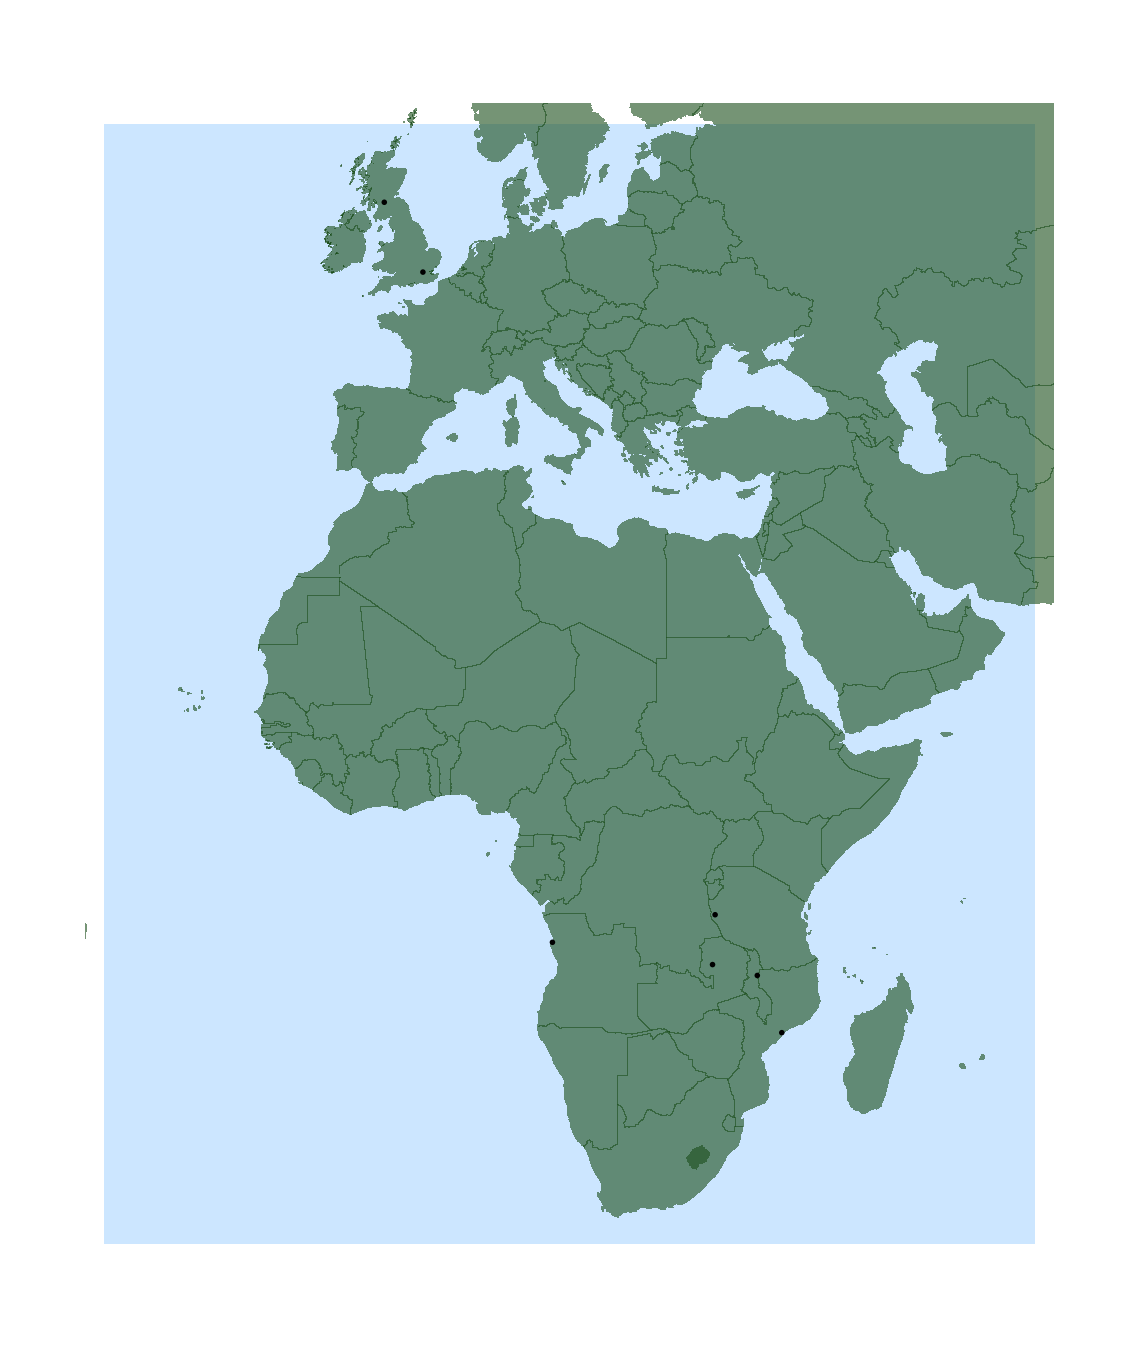

```mathematica
GeoGraphics[{GeoStyling[RGBColor[.1,.3, .1],Opacity[.6]], worldPolygon,GeoStyling[RGBColor[1,.4, .4], Opacity[.6]], livingstoneDisks},GeoBackground->RGBColor[.8, .9, 1], GeoProjection->"Mercator", GeoRange->{{-37., 60.}, {-33., 63.}}]
```